```mathematica
Clear[f,x,y,n,alfa,beta];
alfa = 4;
beta = 9;
n=75;
f[x_,y_] = x*y*ⅇ^(-alfa(x^2+y^2));
{{a,b},{c,d}} = {{0,beta},{0,beta}}; 
△x =(b-a)/n;
△y=(d-c)/n;
x[i_]=a+i*△x; 
y[j_]=c+j*△y;
N[∑_(i=1)^n ∑_(j=1)^n (f[(x[i-1]+x[i])/2,(y[j-1]+y[j])/2]△x △y),5]
N[∫_0^beta ∫_0^beta f[x,y]ⅆxⅆy]
plot = Plot3D[(x y)/E^(4 (x^2+y^2)),{x,0,1.5},{y,0,1.5},PlotRange->Full,AxesLabel->Automatic, Mesh->None,MaxRecursion->10,PlotPoints->50,ColorFunction->Function[{x,y,z},Hue[z]]]
```

0.015777

0.015625

-Graphics3D-

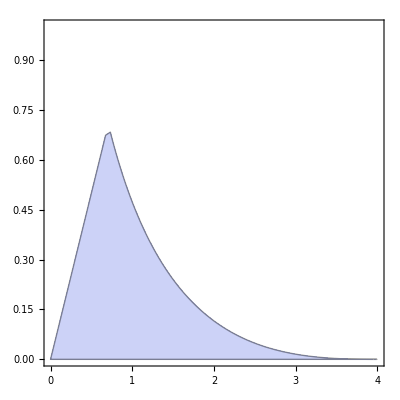

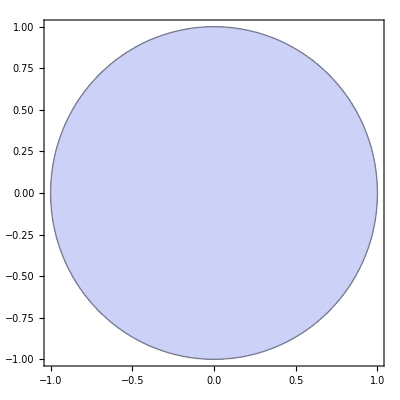

```mathematica
Clear[f,x,y,n];
RegionPlot[x^(2/5)+y^(2/5)≤ alfa^(2/5)&&0≤y≤x,{x,0,4},{y,0,1}]
Clear[f,x,y,n];
RegionPlot[x^2+y^2≤1,{x,-1,1},{y,-1,1}]
```